```mathematica
Clear[p,q,s];
a=1;b=2;
∫_0^(π/2) (c*(Cos[ϕ])^2+d)Sin[ϕ]ⅆϕ
∫_0^(π/2) (c*(Cos[ϕ])^2+d)LegendreP[2,Cos[ϕ]]Sin[ϕ]ⅆϕ
An[n_]:=(4n+1)/(a^(2n)-b^(4n+1)*a^(-1-2n))∫_0^(π/2) (p*(Cos[φ])^4+q*(Cos[φ])^2+s)*LegendreP[2*n,Cos[φ]]*Sin[φ]ⅆφ
```

c/3+d

(2 c)/15

```mathematica
Ann[n_]:=(4n+1)/(a^(2n)-b^(4n+1)*a^(-1-2n))∫_0^(π/2) (uextension[a,φ])*LegendreP[2*n,Cos[φ]]*Sin[φ]ⅆφ
```

```mathematica
An[0]
An[1]
An[2]
An[3]
```

-p/5-q/3-s

-2/651 (6 p+7 q)

-(8 p)/17885

0

```mathematica
An[0]
```

-p/5-q/3-s

```mathematica
An[1]
```

-2/651 (6 p+7 q)

```mathematica
An[2]
```

-(8 p)/17885

```mathematica
An[3]
```

```mathematica
Solve[-p/5-q/3-s==-132/5&&-2/651 (6 p+7 q)==1728/5467&&-(8 p)/17885==-126805794471936/304952288540585,{p,q,s}]
```

{{p→15850724308992/17050729021,q→-10806650612890272/13316619365401,s→1477892485145460/13316619365401}}

```mathematica
Textension[φ_]:=15850724308992/17050729021*(Cos[φ])^4+-10806650612890272/13316619365401*(Cos[φ])^2+1477892485145460/13316619365401
```

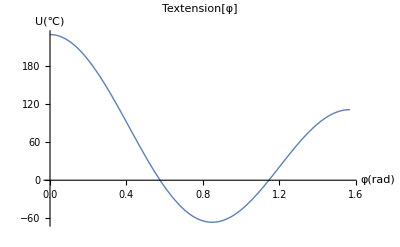

```mathematica
Plot[Textension[φ],{φ,0,π/2},PlotLabel->"Textension[φ]", PlotRange->All,AxesLabel->{"φ(rad)","U(℃)"},BaseStyle->{FontSize->18},PlotStyle->Thick]
```

```mathematica
p=15850724308992/17050729021;q=-10806650612890272/13316619365401;s=1477892485145460/13316619365401
```

1477892485145460/13316619365401

```mathematica
Solve[ -2/3 (c+3 d)==-12&&-(4 c)/93==-864/781,{c,d}]
```

{{c→20088/781,d→-2010/781}}

```mathematica
12+160704/3905
```

207564/3905

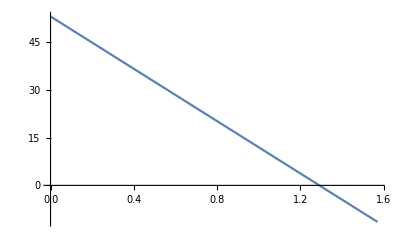

```mathematica
T[ϕ_]:=-160704/3905*ϕ+207564/3905
Plot[T[ϕ],{ϕ,0,π/2}]
```

```mathematica
u[ρ_,ϕ_]:=-12*(ρ^0-b^1*ρ^-1)-864/781*LegendreP[2,Cos[ϕ]]*(-b^5*ρ^-3+ρ^2)
f[ρ_,ϕ_]:=-36*(ρ^0-b^1*ρ^-1)
D[u[ρ,ϕ],ϕ]
u[1,0]
u[(a+b)/2,0]
Plot[u[ρ,0],{ρ,1,2}]
Plot3D[u[ρ,ϕ],{ρ,a,b},{ϕ,0,π/2}]
ContourPlot[u[√(x^2+y^2),ArcTan[y,x]],{x,y}∈Annulus[{0,0},{0.1,2},{0,π/2}],BaseStyle->{FontSize->18},FrameLabel->{"x","y"},ColorFunction->"DarkRainbow",ContourLabels->False,Contours->Range[-20,50,1],PlotLegends->Automatic]
ContourPlot[f[√(x^2+y^2),ArcTan[y,x]],{x,y}∈Annulus[{0,0},{1,2},{0,π/2}],BaseStyle->{FontSize->18},FrameLabel->{"x","y"},ColorFunction->"DarkRainbow",ContourLabels->False,Contours->Range[-20,100,1],PlotLegends->Automatic]
```

2592/781 (-32/ρ^3+ρ^2) Cos[ϕ] Sin[ϕ]

36156/781

```mathematica
N[36156/781]
```

46.2945

```mathematica
(864*31*6)/(5*781)
8/(9/4-32*8/27)
```

```mathematica
u[ρ_,ϕ_]:=-12*(ρ^0-b^1*ρ^-1)-864/781*LegendreP[2,Cos[ϕ]]*(-b^5*ρ^-3+ρ^2)
```

```mathematica
u[1.5,0]
```

12.

```mathematica
LegendreP[4,Cos[φ]]
```

1/8 (3-30 Cos[φ]^2+35 Cos[φ]^4)

```mathematica
∫_0^(π/2) Cos[((2n-1)x)^2]ⅆx
```

(√(π/2) FresnelC[(-1+2 n) √(π/2)])/(-1+2 n)

```mathematica
Solve[B0*(ρ^0-b^1*ρ^-1)+B1*LegendreP[2,Cos[0]]*(-b^5*ρ^-3+ρ^2)+B2*LegendreP[4,Cos[0]]*(-b^17*ρ^-9+ρ^8)==12&&B0*(ρ^0-b^1*ρ^-1)+B1*LegendreP[2,Cos[π/4]]*(-b^5*ρ^-3+ρ^2)+B2*LegendreP[4,Cos[π/4]]*(-b^17*ρ^-9+ρ^8)==6&&B0*(ρ^0-b^1*ρ^-1)+B1*LegendreP[2,Cos[π/8]]*(-b^5*ρ^-3+ρ^2)+B2*LegendreP[4,Cos[π/8]]*(-b^17*ρ^-9+ρ^8)==9,{B0,B1,B2}]
```

{{B0→-(6 (19-42 Cos[π/8]^2+20 Cos[π/8]^4))/(5 (1-3 Cos[π/8]^2+2 Cos[π/8]^4)),B1→-(216 (1-48 Cos[π/8]^2+56 Cos[π/8]^4))/(5467 (1-3 Cos[π/8]^2+2 Cos[π/8]^4)),B2→(241864704 (-3+4 Cos[π/8]^2))/(596775515735 (1-3 Cos[π/8]^2+2 Cos[π/8]^4))}}

```mathematica
N[1728/5467-(-(216 (1-48 Cos[π/8]^2+56 Cos[π/8]^4))/(5467 (1-3 Cos[π/8]^2+2 Cos[π/8]^4)))]
```

-1.38778×10^-15

```mathematica
uextension[ρ_,φ_]:=-(6 (19-42 Cos[π/8]^2+20 Cos[π/8]^4))/(5 (1-3 Cos[π/8]^2+2 Cos[π/8]^4))*(ρ^0-b^1*ρ^-1)-(216 (1-48 Cos[π/8]^2+56 Cos[π/8]^4))/(5467 (1-3 Cos[π/8]^2+2 Cos[π/8]^4))*LegendreP[2,Cos[φ]]*(-b^5*ρ^-3+ρ^2)+(241864704 (-3+4 Cos[π/8]^2))/(596775515735 (1-3 Cos[π/8]^2+2 Cos[π/8]^4))(-b^17*ρ^-9+ρ^8)*LegendreP[4,Cos[φ]]
```

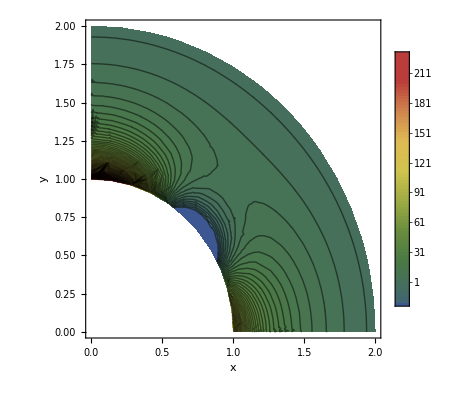

```mathematica
ContourPlot[uextension[√(x^2+y^2),ArcTan[y,x]],{x,y}∈Annulus[{0,0},{1,2},{0,π/2}],BaseStyle->{FontSize->18},FrameLabel->{"x","y"},ColorFunction->"DarkRainbow",ContourLabels->False,Contours->Range[-20,560,3],PlotRange->All,PlotLegends->Automatic]
```

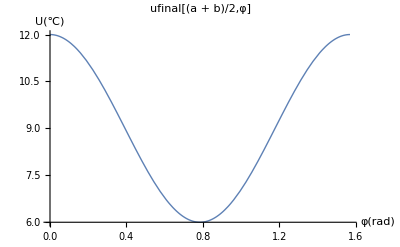

```mathematica
Plot[uextension[(a+b)/2,φ],{φ,0,π/2},PlotLabel->"ufinal[(a + b)/2,φ]", PlotRange->All,AxesLabel->{"φ(rad)","U(℃)"},BaseStyle->{FontSize->18},PlotStyle->Thick]
```

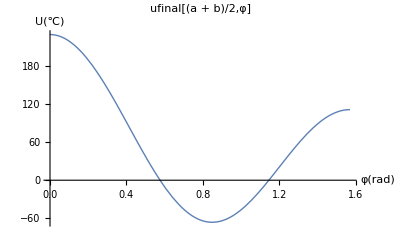

```mathematica
Plot[uextension[a,φ],{φ,0,π/2},PlotLabel->"ufinal[(a + b)/2,φ]", PlotRange->All,AxesLabel->{"φ(rad)","U(℃)"},BaseStyle->{FontSize->18},PlotStyle->Thick]
```

```mathematica
N[uextension[a,0]]
```

229.086

```mathematica
uextension[a,φ]
```

(6 (19-42 Cos[π/8]^2+20 Cos[π/8]^4))/(5 (1-3 Cos[π/8]^2+2 Cos[π/8]^4))+(3348 (1-48 Cos[π/8]^2+56 Cos[π/8]^4) (-1+3 Cos[φ]^2))/(5467 (1-3 Cos[π/8]^2+2 Cos[π/8]^4))-(3962681077248 (-3+4 Cos[π/8]^2) (3-30 Cos[φ]^2+35 Cos[φ]^4))/(596775515735 (1-3 Cos[π/8]^2+2 Cos[π/8]^4))